In this notebook we derive some of the mathematical tools we used to analyze the adaptive dynamics of our model. In particular, we derive explicit expressions for invasion fitness, for the selection gradient and for the curvature of the fitness function. Other derivations are presented in the manuscript.

The model

The model is as follows:

```mathematica
(* Transition matrix *)
Λ=S.M.R;

(* Establishment matrix *)
S=({{Subscript[s, 1], 0}, {0, Subscript[s, 2]}});

(* Migration matrix *)
M=({{c+ϕ(1-c), c(1-ϕ)}, {(1-c)(1-ϕ), (1-c)+ϕ c}});

(* Birth matrix *)
R=({{Subscript[r, 1], 0}, {0, Subscript[r, 2]}});

(* Density-dependent birth *)
Subscript[r, 1][x_]:=Exp[(Subscript[r, max]-ϵ x)(1-Subscript[n, 1]/(c Subscript[k, 1]))];
Subscript[r, 2][x_]:=Exp[(Subscript[r, max]-ϵ x)(1-Subscript[n, 2]/((1-c) Subscript[k, 2]))];

(* Germination *)
Subscript[s, 1][x_]:=1/(1+Exp[a(Subscript[θ, 1]-x)]);
Subscript[s, 2][x_]:=1/(1+Exp[a(Subscript[θ, 2]-x)]);
```

#### Population dynamics

Here we have a look at what the population dynamics of our model look like under a fixed set of parameters, e.g.

```mathematica
(* Example parameter set *)
pars={Subscript[k, 1]->2000,Subscript[k, 2]->1000,Subscript[r, max]->1,ϵ->0.1,a->5,Subscript[θ, 1]->0,Subscript[θ, 2]->0,c->0.5,ϕ->0};
```

We then evaluate the population densities in the two patches at various time steps given a trait value and some initial conditions.

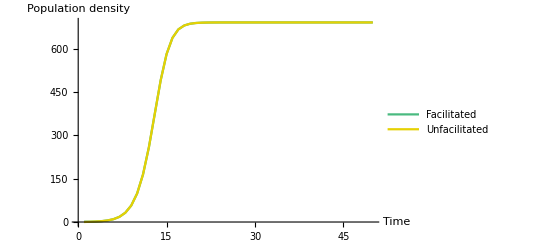

```mathematica
(* Rules to make explicit *)
expl={Subscript[s, 1]->Subscript[s, 1][x],Subscript[s, 2]->Subscript[s, 2][x],Subscript[r, 1]->Subscript[r, 1][x],Subscript[r, 2]->Subscript[r, 2][x]};

(* Equations describing the dynamics *)
eq={Subscript[n, 1][t+1],Subscript[n, 2][t+1]}==(Λ/.expl/.{Subscript[n, 1]->Subscript[n, 1][t],Subscript[n, 2]->Subscript[n, 2][t]}).{Subscript[n, 1][t],Subscript[n, 2][t]}/.pars/.x->4;

(* Initial conditions *)
init={Subscript[n, 1][0]==1,Subscript[n, 2][0]==0};

(* Numerical evaluation *)
tab=RecurrenceTable[{eq,init},{Subscript[n, 1],Subscript[n, 2]},{t,0,49}];

(* Plotting *)
ListLinePlot[Transpose[tab],PlotStyle->{RGBColor[0.29,0.73,0.5],RGBColor[0.9,0.82,0.01]},PlotRange->Full,PlotLegends->{"Facilitated","Unfacilitated"},AxesLabel->{"Time","Population density"}]
```

### Invasion fitness

Next, we compute the invasion fitness of the mutant as the leading eigenvalue of the transition matrix.

```mathematica
λ=Λ//Eigenvalues//Last
```

1/2 (c r_1 s_1+ϕ r_1 s_1-c ϕ r_1 s_1+r_2 s_2-c r_2 s_2+c ϕ r_2 s_2+√(-4 ϕ r_1 r_2 s_1 s_2+(-c r_1 s_1-ϕ r_1 s_1+c ϕ r_1 s_1-r_2 s_2+c r_2 s_2-c ϕ r_2 s_2)^2))

We now check that the invasion fitness is indeed one when evaluated at the resident, i.e. when the mutant is the resident, under a random set of parameter values. For this we need to find the equilibrium population densities given the parameters (we do that numerically).

```mathematica
(* Find equilibrium densities *)
eq={Subscript[n, 1],Subscript[n, 2]}==Λ.{Subscript[n, 1],Subscript[n, 2]}/.expl;
sol=FindRoot[eq/.pars/.x->4,{{Subscript[n, 1],1000},{Subscript[n, 2],1000}}]
```

{n_1→690.326,n_2→690.326}

Then, we plug those equilibrium densities into the invasion fitness function, with the rest of the parameters.

```mathematica
(* Invasion fitness of the resident *)
λ/.expl/.pars/.sol/.x->4
```

1.

Now that we have the invasion fitness, we want to get a formula for the selection gradient, which will help us identify singular strategies and long-term evolutionary equilibria.

### Selection gradient

We know that the selection gradient can be expressed in terms of the derivative of the transition matrix (here dΛ) and the left and right dominant eigenvectors (v and u, respectively) of said matrix (Otto and Day), as such:

```mathematica
(* Selection gradient *)
G=v.dΛ.u/(v.u);
```

which we can express in terms of the derivatives of the fitness function in each patch, w_1 and w_2, respectively,

```mathematica
(* Derivative of the transition matrix *)
dΛ=S.M.dR+dS.M.R;

(* Derivative of the survival matrix *)
dS=({{Subscript[ds, 1], 0}, {0, Subscript[ds, 2]}});
Subscript[ds, 1][x_]:=a Subscript[s, 1][x](1-Subscript[s, 1][x]);
Subscript[ds, 2][x_]:=a Subscript[s, 2][x](1-Subscript[s, 2][x]);

(* Derivative of the reproduction matrix *)
dR=({{Subscript[dr, 1], 0}, {0, Subscript[dr, 2]}});
Subscript[dr, 1][x_]:=ϵ(Subscript[n, 1]/Subscript[k, 1]-1)Subscript[r, 1][x];
Subscript[dr, 2][x_]:=ϵ(Subscript[n, 2]/Subscript[k, 2]-1)Subscript[r, 2][x];
```

We can now identify a pair of possible left and right eigenvectors for the transition matrix:

```mathematica
(* Left and right eigenvectors *)
left=(Λ//Eigenvectors//Last)
right=(Λ//Transpose//Eigenvectors//Last)
```

{-1/(2 (-1+c) (-1+ϕ) r_1 s_2)(-c r_1 s_1-ϕ r_1 s_1+c ϕ r_1 s_1+r_2 s_2-c r_2 s_2+c ϕ r_2 s_2-√(c^2 r_1^2 s_1^2+2 c ϕ r_1^2 s_1^2-2 c^2 ϕ r_1^2 s_1^2+ϕ^2 r_1^2 s_1^2-2 c ϕ^2 r_1^2 s_1^2+c^2 ϕ^2 r_1^2 s_1^2+2 c r_1 r_2 s_1 s_2-2 c^2 r_1 r_2 s_1 s_2-2 ϕ r_1 r_2 s_1 s_2-4 c ϕ r_1 r_2 s_1 s_2+4 c^2 ϕ r_1 r_2 s_1 s_2+2 c ϕ^2 r_1 r_2 s_1 s_2-2 c^2 ϕ^2 r_1 r_2 s_1 s_2+r_2^2 s_2^2-2 c r_2^2 s_2^2+c^2 r_2^2 s_2^2+2 c ϕ r_2^2 s_2^2-2 c^2 ϕ r_2^2 s_2^2+c^2 ϕ^2 r_2^2 s_2^2)),1}

{-1/(2 c (-1+ϕ) r_2 s_1)(c r_1 s_1+ϕ r_1 s_1-c ϕ r_1 s_1-r_2 s_2+c r_2 s_2-c ϕ r_2 s_2+√(c^2 r_1^2 s_1^2+2 c ϕ r_1^2 s_1^2-2 c^2 ϕ r_1^2 s_1^2+ϕ^2 r_1^2 s_1^2-2 c ϕ^2 r_1^2 s_1^2+c^2 ϕ^2 r_1^2 s_1^2+2 c r_1 r_2 s_1 s_2-2 c^2 r_1 r_2 s_1 s_2-2 ϕ r_1 r_2 s_1 s_2-4 c ϕ r_1 r_2 s_1 s_2+4 c^2 ϕ r_1 r_2 s_1 s_2+2 c ϕ^2 r_1 r_2 s_1 s_2-2 c^2 ϕ^2 r_1 r_2 s_1 s_2+r_2^2 s_2^2-2 c r_2^2 s_2^2+c^2 r_2^2 s_2^2+2 c ϕ r_2^2 s_2^2-2 c^2 ϕ r_2^2 s_2^2+c^2 ϕ^2 r_2^2 s_2^2)),1}

If we now rescale the eigenvectors slightly...

```mathematica
left=left m Subscript[r, 1] Subscript[s, 2]
right=right m Subscript[r, 2] Subscript[s, 1]
```

{-1/(2 (-1+c) (-1+ϕ))m (-c r_1 s_1-ϕ r_1 s_1+c ϕ r_1 s_1+r_2 s_2-c r_2 s_2+c ϕ r_2 s_2-√(c^2 r_1^2 s_1^2+2 c ϕ r_1^2 s_1^2-2 c^2 ϕ r_1^2 s_1^2+ϕ^2 r_1^2 s_1^2-2 c ϕ^2 r_1^2 s_1^2+c^2 ϕ^2 r_1^2 s_1^2+2 c r_1 r_2 s_1 s_2-2 c^2 r_1 r_2 s_1 s_2-2 ϕ r_1 r_2 s_1 s_2-4 c ϕ r_1 r_2 s_1 s_2+4 c^2 ϕ r_1 r_2 s_1 s_2+2 c ϕ^2 r_1 r_2 s_1 s_2-2 c^2 ϕ^2 r_1 r_2 s_1 s_2+r_2^2 s_2^2-2 c r_2^2 s_2^2+c^2 r_2^2 s_2^2+2 c ϕ r_2^2 s_2^2-2 c^2 ϕ r_2^2 s_2^2+c^2 ϕ^2 r_2^2 s_2^2)),m r_1 s_2}

{-1/(2 c (-1+ϕ))m (c r_1 s_1+ϕ r_1 s_1-c ϕ r_1 s_1-r_2 s_2+c r_2 s_2-c ϕ r_2 s_2+√(c^2 r_1^2 s_1^2+2 c ϕ r_1^2 s_1^2-2 c^2 ϕ r_1^2 s_1^2+ϕ^2 r_1^2 s_1^2-2 c ϕ^2 r_1^2 s_1^2+c^2 ϕ^2 r_1^2 s_1^2+2 c r_1 r_2 s_1 s_2-2 c^2 r_1 r_2 s_1 s_2-2 ϕ r_1 r_2 s_1 s_2-4 c ϕ r_1 r_2 s_1 s_2+4 c^2 ϕ r_1 r_2 s_1 s_2+2 c ϕ^2 r_1 r_2 s_1 s_2-2 c^2 ϕ^2 r_1 r_2 s_1 s_2+r_2^2 s_2^2-2 c r_2^2 s_2^2+c^2 r_2^2 s_2^2+2 c ϕ r_2^2 s_2^2-2 c^2 ϕ r_2^2 s_2^2+c^2 ϕ^2 r_2^2 s_2^2)),m r_2 s_1}

... we see that they can be rewritten in terms of λ:

```mathematica
left[[1]]-λ//Simplify
right[[1]]-λ//Simplify
```

1/2 (-c r_1 s_1-ϕ r_1 s_1+c ϕ r_1 s_1-r_2 s_2+c r_2 s_2-c ϕ r_2 s_2-√(-4 ϕ r_1 r_2 s_1 s_2+((c (-1+ϕ)-ϕ) r_1 s_1+(-1+c-c ϕ) r_2 s_2)^2)+1/((-1+c) (-1+ϕ))m (c r_1 s_1+ϕ r_1 s_1-c ϕ r_1 s_1-r_2 s_2+c r_2 s_2-c ϕ r_2 s_2+√(-4 ϕ r_1 r_2 s_1 s_2+((c (-1+ϕ)-ϕ) r_1 s_1+(-1+c-c ϕ) r_2 s_2)^2)))

-1/(2 c (-1+ϕ))(-c^2 r_1 s_1+c m r_1 s_1-c ϕ r_1 s_1+2 c^2 ϕ r_1 s_1+m ϕ r_1 s_1-c m ϕ r_1 s_1+c ϕ^2 r_1 s_1-c^2 ϕ^2 r_1 s_1-c r_2 s_2+c^2 r_2 s_2-m r_2 s_2+c m r_2 s_2+c ϕ r_2 s_2-2 c^2 ϕ r_2 s_2-c m ϕ r_2 s_2+c^2 ϕ^2 r_2 s_2-c √(-4 ϕ r_1 r_2 s_1 s_2+((c (-1+ϕ)-ϕ) r_1 s_1+(-1+c-c ϕ) r_2 s_2)^2)+m √(-4 ϕ r_1 r_2 s_1 s_2+((c (-1+ϕ)-ϕ) r_1 s_1+(-1+c-c ϕ) r_2 s_2)^2)+c ϕ √(-4 ϕ r_1 r_2 s_1 s_2+((c (-1+ϕ)-ϕ) r_1 s_1+(-1+c-c ϕ) r_2 s_2)^2))

Such that

```mathematica
λ-(1-m)Subscript[r, 2] Subscript[s, 2]==left[[1]]==right[[1]]//Simplify
```

1/2 (c r_1 s_1+ϕ r_1 s_1-c ϕ r_1 s_1-r_2 s_2-c r_2 s_2+2 m r_2 s_2+c ϕ r_2 s_2+√(-4 ϕ r_1 r_2 s_1 s_2+((c (-1+ϕ)-ϕ) r_1 s_1+(-1+c-c ϕ) r_2 s_2)^2))==1/(2 (-1+c) (-1+ϕ))m (c r_1 s_1+ϕ r_1 s_1-c ϕ r_1 s_1-r_2 s_2+c r_2 s_2-c ϕ r_2 s_2+√((c+ϕ-c ϕ)^2 r_1^2 s_1^2-2 (-c (-1+ϕ)^2+c^2 (-1+ϕ)^2+ϕ) r_1 r_2 s_1 s_2+(1+c (-1+ϕ))^2 r_2^2 s_2^2))==-1/(2 c (-1+ϕ))m (c r_1 s_1+ϕ r_1 s_1-c ϕ r_1 s_1-r_2 s_2+c r_2 s_2-c ϕ r_2 s_2+√((c+ϕ-c ϕ)^2 r_1^2 s_1^2-2 (-c (-1+ϕ)^2+c^2 (-1+ϕ)^2+ϕ) r_1 r_2 s_1 s_2+(1+c (-1+ϕ))^2 r_2^2 s_2^2))

And so, we use the following expressions for these two eigenvectors:

```mathematica
left[[1]]=λ-(1-m)Subscript[r, 2] Subscript[s, 2];
right[[1]]=λ-(1-m)Subscript[r, 2] Subscript[s, 2];
```

We can now get an expression for the selection gradient by substituting those in the previous formula, and evaluating the result at the resident (i.e. when λ = 1).

```mathematica
G=G/.u->left/.v->right/.λ->1//Simplify
```

(ds_1 r_1 (1-m-(2-4 m+m^2) r_2 s_2+(1-3 m+2 m^2) r_2^2 s_2^2)+s_1 (m^2 r_1 (ds_2 r_2+dr_2 s_2)+dr_1 (1-m-(2-4 m+m^2) r_2 s_2+(1-3 m+2 m^2) r_2^2 s_2^2)))/(1+r_2 (-2+2 m+m^2 r_1 s_1) s_2+(-1+m)^2 r_2^2 s_2^2)

We could also have obtained a selection gradient by differentiating the invasion fitness function directly, but this would take a lot of computation time, especially if (as we shall see) we have to repeat this numerically for many possible combinations of parameters. That said, we can compare the expression we just derived to that more “brute-force” approach, to make sure our selection gradient is correct, given the same parameter values (and demographic equilibria) we have tried before.

```mathematica
(* Differentiate the invasion fitness *)
diff=D[λ/.expl,x];
```

This gives a lengthy expression, unpractical for high-throughput numerical evaluation...

```mathematica
diff; (* Remove ";" to see *)
```

When evaluated at the resident previously tested, that gives

```mathematica
(* Evaluate at resident *)
diff/.pars/.sol/.x->4
```

0.903698

Now we compare with the (shorter) formula for the fitness gradient.

```mathematica
(* Rules to make derivatives explicit *)
dexpl={Subscript[ds, 1]->Subscript[ds, 1][x],Subscript[ds, 2]->Subscript[ds, 2][x],Subscript[dr, 1]->Subscript[dr, 1][x],Subscript[dr, 2]->Subscript[dr, 2][x]};

(* Evaluation of the selection gradient formula *)
G/.expl/.dexpl/.pars/.sol/.x->4
```

0.903698

### Singular strategies

There may be values of trait x for which the selection gradient becomes zero. Those are termed evolutionary singular strategies, evolutionary steady-states or evolutionary equilibria. We could not find such values analytically because the value of the selection gradient at a given trait value depends on the equilibrium size of the population given that trait value, and there is no explicit expression for that (above we had to find the demographic equilibrium through numerical root finding). Hence, here we solved for the roots of the selection gradient numerically, under various sets of parameters. We did this elsewhere, as this notebook is primarily about showing the derivations of the mathematical expressions we used.

### Evolutionary stability

Once a singular strategy has been found, it is not guaranteed that this is an endpoint of evolution. For this, the singularity must be evolutionarily stable, that is, once the population is there, it does not evolve away. Mathematically, this happens when the second derivative of the invasion fitness with respect to the mutant trait value is negative when evaluated at the singularity. So, the criterion for evolutionary stability (or invasion-proofness) involves the curvature of the invasion fitness function. It can be shown (see Appendix) that this curvature, when evaluated at a singular strategy, is

```mathematica
(* Fitness curvature *)
F=(dv.dΛ.u+v.ddΛ.u+v.dΛ.du)/(v.u);
```

where d symbolizes a derivative and dd symbolizes the second derivative (of the transition matrix in the case of ddΛ).

We can show that at equilibrium, the derivatives of vectors u and v are

```mathematica
(* Derivatives of the eigenvectors *)
dleft={(m-1)(Subscript[r, 2] Subscript[ds, 2]+Subscript[dr, 2] Subscript[s, 2]),m (Subscript[r, 1] Subscript[ds, 2]+Subscript[dr, 2] Subscript[s, 2])};
dright={(m-1)(Subscript[r, 2] Subscript[ds, 2]+Subscript[dr, 2] Subscript[s, 2]),m (Subscript[r, 2] Subscript[ds, 1]+Subscript[dr, 2] Subscript[s, 1])};
```

We can also express the second derivative of the transition matrix as such:

```mathematica
(* Second derivative of the transition matrix *)
ddΛ=ddS.M.R+2.dS.M.dR+S.M.ddR;

(* Second derivative of the survival matrix *)
ddS=({{Subscript[dds, 1], 0}, {0, Subscript[dds, 2]}});
Subscript[dds, 1][x_]:=a(1-2 Subscript[s, 1][x])Subscript[ds, 1][x];
Subscript[dds, 2][x_]:=a(1-2 Subscript[s, 2][x])Subscript[ds, 2][x];

(* Second derivative of the reproduction matrix *)
ddR=({{Subscript[ddr, 1], 0}, {0, Subscript[ddr, 2]}});
Subscript[ddr, 1][x_]:=ϵ(Subscript[n, 1]/Subscript[k, 1]-1)Subscript[dr, 1][x];
Subscript[ddr, 2][x_]:=ϵ(Subscript[n, 2]/Subscript[k, 2]-1)Subscript[dr, 2][x];
```

Now we can substitute the above into the expression for the fitness curvature at equilibrium, and simplify, which gives us

```mathematica
F/.u->left/.v->right/.du->dleft/.dv->dright/.λ->1//Simplify
```

(m^2 (ds_2 r_1+dr_2 s_2) ((dr_2-(-1+m) ds_2 r_2^2) s_1+ds_1 r_2 (1+(-1+m) r_2 s_2))+(1+(-1+m) r_2 s_2) (m^2 r_1 (2. dr_2 ds_1+dds_1 r_2+ddr_2 s_1) s_2+(1-m) (2. dr_1 ds_1+dds_1 r_1+ddr_1 s_1) (1+(-1+m) r_2 s_2))+(-1+m) (ds_2 r_2+dr_2 s_2) (m^2 r_1 (ds_1 r_2+dr_2 s_1) s_2-(-1+m) (ds_1 r_1+dr_1 s_1) (1+(-1+m) r_2 s_2))+(-1+m) (ds_2 r_2+dr_2 s_2) (m^2 r_2 s_1 (ds_2 r_1+dr_1 s_2)-(-1+m) (ds_1 r_1+dr_1 s_1) (1+(-1+m) r_2 s_2))+m r_2 s_1 (-1. (-1.+m) m r_1 s_2 (2. dr_2 ds_2+dds_2 r_2+ddr_2 s_2)+m (2. dr_1 ds_2+dds_2 r_1+ddr_1 s_2) (1+(-1+m) r_2 s_2))+m^2 (ds_1 r_2+dr_2 s_1) (ds_2 r_1+s_2 (-(-1+m) dr_2 r_1 s_2+dr_1 (1+(-1+m) r_2 s_2))))/(m^2 r_1 r_2 s_1 s_2+(1+(-1+m) r_2 s_2)^2)

As for the selection gradient above, we could check the validity of this formula by comparing it to brute-force second-differentiation of the invasion fitness, but we need to do it at a singular strategy, that is, when the selection gradient is zero. This means that we first have to find one potential such equilibrium.

Again, the selection gradient depends on equilibrium population sizes, and there is no explicit expression for those, so we could not solve the root of the selection gradient analytically. Instead, we numerically solved a system of equations to find the combination of x and population sizes that simultaneously solve both the demographic equilibrium (population does not change size anymore) and the evolutionary equilibrium (selection gradient is zero).  We did this as follows:

```mathematica
(* System of equations to solve *)
eqs={{Subscript[n, 1],Subscript[n, 2]}==Λ. {Subscript[n, 1],Subscript[n, 2]},G==0}/.expl/.dexpl;

(* Solve numerically *)
sol=FindRoot[eqs/.pars,{{Subscript[n, 1],1000},{Subscript[n, 2],1000},{x,1}}]
```

{n_1→2982.09,n_2→0.000253835,x→0.739256}

Now that we have a candidate singular strategy, we can double-differentiate the invasion fitness function from scratch to get an expression for the curvature, and evaluate it at the singularity.

```mathematica
(* Brute-force differentiation *)
diff2=D[diff,x];

(* Evaluate at equilibrium *)
diff2/.pars/.sol
```

-0.590704

We can now compare that value with that obtained from our derived formula for the curvature:

```mathematica
(* Rules to make second derivatives explicit *)
ddexpl={Subscript[dds, 1]->Subscript[dds, 1][x],Subscript[dds, 2]->Subscript[dds, 2][x],Subscript[ddr, 1]->Subscript[ddr, 1][x],Subscript[ddr, 2]->Subscript[ddr, 2][x]};

(* Evaluate the curvature of the fitness function *)
F/.dv->dright/.du->dleft/.v->right/.u->left/.expl/.dexpl/.ddexpl/.pars/.sol
```

-0.590703

(Those should be the same.)

### Convergence stability

We just derived an expression for the curvature of the invasion fitness function, which allows us to evaluate whether a given singularity (trait value such that the selection gradient is zero) is evolutionarily stable, or invasion-proof. However, evolutionary stability only means that a trait value will stay where it is once the population is at the singularity, but it does not say whether evolution will lead to that singularity in the first place. Whether a singular strategy is attainable has to do with convergence stability, and for a singular strategy to be convergence-stable, the requirement is that the selection gradient is negative for trait values that are above the singularity, and positive for trait values that are below the singularity (i.e. the selection gradient leads towards the singularity). Mathematically, this means that the derivative of the selection gradient with respect to the resident strategy must be negative when evaluated at the singular point. This is different from the curvature of the fitness function, which is the second derivative of the invasion fitness with respect to the mutant, which is then evaluated at the singularity. As we explain in the manuscript, we could not come up with an explicit expression for the derivative of the selection gradient with respect to the resident trait value, because as the resident trait value changes the demographic equilibrium also changes, such that differentiating the selection gradient requires involves the derivatives of those equilibrium population sizes, for which we do not have an explicit expression. Hence, for all intents and purposes we used numerical evaluation of the selection gradient around singularities to estimate whether said singularity was convergence-stable.